## Jackson 7.19

### Part b

Our function for this problem is

```mathematica
f = N0 E^(-α^2 x^2/4);
```

The energy density is

```mathematica
u0 = f E^(I k0 x);
```

The amplitude of the wavenumber spectrum is given by

```mathematica
A[u_] := 1/(√(2 π))Integrate[u E^(-I k x),{x, -Infinity, Infinity}];
```

Plug in our energy density

```mathematica
Ab = FullSimplify[A[u0], Assumptions->α ∈ Reals && α > 0]
```

$Aborted

Evaluate the wavenumber spectrum

```mathematica
kSpec = Ab^2
```

(2 ⅇ^(-(2 (k-k0)^2)/α^2) N0^2)/α^2

Plot the wavenumber spectrum

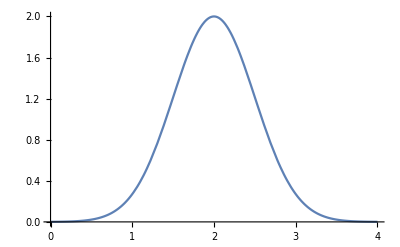

```mathematica
Plot[kSpec/. k0-> 2α /. α -> 1/. N0-> 1,{k,0,4}]
```

Evaluate the modulus squared of the energy density

```mathematica
uSpec = FullSimplify[Abs[u0]^2, Assumptions->N0 >0 && α >0 && x ∈ Reals && k0 ∈ Reals]
```

ⅇ^(-1/2 x^2 α^2) N0^2

Plot the modulus squared of the energy density

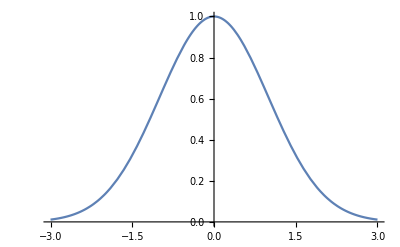

```mathematica
Plot[uSpec/. α -> 1/. N0-> 1,{x,-3,3}]
```

Find the spread in the wavenumber

```mathematica
Δk =FullSimplify[ √(Integrate[k^2 kSpec,{k,-Infinity,Infinity}]/Integrate[kSpec,{k,-Infinity,Infinity}]),Assumptions->α > 0]
```

1/2 √(4 k0^2+α^2)

```mathematica
Δx =FullSimplify[ √(Integrate[x^2 uSpec,{x,-Infinity,Infinity}]/Integrate[uSpec,{x,-Infinity,Infinity}]),Assumptions->α > 0]
```

1/α

### Part c

Our function for this problem is

```mathematica
f = N0( -HeavisideTheta[x-a] + HeavisideTheta[x+a]);
Plot[f /. N0-> 1 /.a-> 1,{x,-2,2}];
```

The energy density is

```mathematica
u0 = f E^(I k0 x);
```

Plug in our energy density

```mathematica
Ac = FullSimplify[A[u0], Assumptions->Im[k0]> Im[k]]
```

(N0 √(2/π) Sin[a (k-k0)])/(k-k0)

Evaluate the wavenumber spectrum

```mathematica
kSpec = Ac^2
```

(2 N0^2 Sin[a (k-k0)]^2)/((k-k0)^2 π)

Plot the wavenumber spectrum

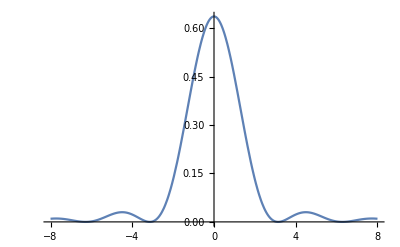

```mathematica
Plot[kSpec/. k0-> 0/. a -> 1/. N0-> 1,{k,-8,8}]
```

Evaluate the modulus squared of the energy density

```mathematica
(uSpec = FullSimplify[Abs[u0]^2, Assumptions->N0 >0 && a >0 && x ∈ Reals && k0 ∈ Reals])//TraditionalForm
```

N0^2 Abs[x-a-a+x]^2

Plot the modulus squared of the energy density

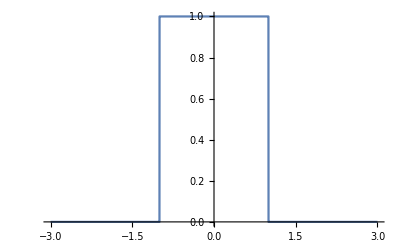

```mathematica
Plot[uSpec/. a -> 1/. N0-> 1,{x,-3,3}]
```

Find the spread in the wavenumber

```mathematica
Δk =FullSimplify[ √(Integrate[ k^2 kSpec/. k0-> 0,{k,-Infinity,Infinity}]/Integrate[kSpec/. k0-> 0,{k,-Infinity,Infinity}])]
```

Integrate::idiv: Integral of (2 N0^2 Sin[a k]^2)/π does not converge on {-∞,∞}.

ConditionalExpression[(√((∫_(-∞)^∞ (2 N0^2 Sin[a k]^2)/π ⅆk)/N0^2))/(√2 √Abs[a]),a∈Reals]

```mathematica
Δx =FullSimplify[ √(Integrate[x^2 uSpec,{x,-Infinity,Infinity}]/Integrate[uSpec,{x,-Infinity,Infinity}])]
```

(√(a^2))/(√3)